# Neural Logic

```mathematica
Get["neural-logic.m",Path->NotebookDirectory[]];
```

```mathematica
?neurallogic`*
```

## Learn XOR

## Generate training data

```mathematica
numBooleanVariables=10;
Echo[2^numBooleanVariables];
bf=BooleanConvert[Xor[#1,#2,#3,#4,#5,#6,#7,#8,#9,#10]&,"BooleanFunction"];
maxExamples=200;
examples=Map[With[{x=RandomChoice[{0,1},numBooleanVariables]},Soften/@x->{Soften[Boole[bf@@x]]}]&,Range[maxExamples]];
{trainData,testData}=[examples,"TestSetSize"->Scaled[0.2],"Shuffle"->True];
```

1024

## Create BNN

```mathematica
{softNet,hardNet}=BinaryNN[{NeuralDNFLayer[numBooleanVariables,200,50],NeuralDNFLayer[50,50,1]}];
```

```mathematica
bnn=AppendLoss[softNet]
```

NetGraph[<>]

## Train BNN

```mathematica
{trainedBNN,resultsObject}=NetTrain[bnn,trainData,{"TrainedNet","ResultsObject"},
ValidationSet->testData,
LossFunction->"Loss",
Method->{"ADAM"},
LearningRate->0.01,
MaxTrainingRounds->10000];
```

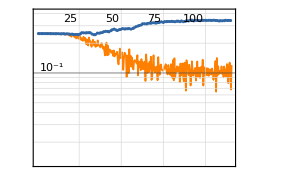
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:2314  rounds:115  time:11min  examples/s:28.
data | ,,  training examples:160  validation examples:40  processed examples:18512  skipped examples:0
method | ,,  ADAMoptimizer  batch size8CPU
round | ,,  loss:1.03×10^-1
validation | ,,  loss:3.39×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
resultsObject
```

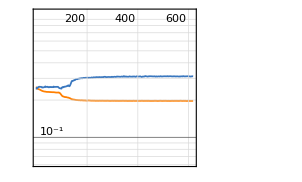
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:3092  rounds:618  time:4.6min  examples/s:405
data | ,,  training examples:160  validation examples:40  processed examples:111312  skipped examples:0
method | ,,  ADAMoptimizer  batch size36CPU
round | ,,  loss:1.97×10^-1
validation | ,,  loss:3.11×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
resultsObject
```

## Evaluate

```mathematica
resultsObject["RoundMeasurements"]
trainedNet=NetExtract[trainedBNN,"NeuralLogicNet"];
```

<|Loss→0.103408|>

### Evaluate soft net

```mathematica
randomTestSample=RandomSample[testData,UpTo[10000]];
softPredictionTargetPairs=[{trainedNet[First[#]],First[Last[#]]}&,randomTestSample];
softPredictionTargetPairs={Harden[#[[1]]],#[[2]]}&/@softPredictionTargetPairs;
Reverse[Sort[Counts[softPredictionTargetPairs]]]
```

<|{{False},0.}→18,{{False},1.}→11,{{True},0.}→6,{{True},1.}→5|>

### Evaluate hard net

```mathematica
trainedBinaryNN=HardBinaryNN[hardNet,trainedNet];
```

```mathematica
hardPredictionTargetPairs=[{First[trainedBinaryNN@@Harden[First[#]]],Harden[First[Last[#]]]}&,randomTestSample];
Sort[Counts[hardPredictionTargetPairs]]
```

<|{False,True}→2,{False,False}→44,{True,True}→54|>

```mathematica
Block[{weights=Flatten[Harden[ExtractWeights[trainedNet]]],bytes,bits},
bytes=Length[weights]/8.0;
bits=StringJoin[ToString/@Boole/@weights];
{bits,Quantity[bytes,"Bytes"],Quantity[bytes/1000.0,"Kilobytes"]}
]
```

{0010010101111011000111110011100100010100100000111001011110100111111000011000010100100001110001011010100000011001011110111101111001001110110001011010000110001101000111001011111000111111001101111001100000010110000011100000001011001111010100101100001110101110101011101110100010001111110100001000001110011001111100111101001100000111101010111100110101010110000010100101110011110100000101100110100010100100000000010011111000010100001111111010011001110100011001111101110001000000101110101100010011101111110000110000001111010111111110110001000100111000111111,68.75 B,0.06875 kB}

```mathematica
trainedBinaryNN;
```

## Learn MNIST

## Generate training data

```mathematica
ConvertBinaryStringToList[s_String]:=ToExpression["{"<>StringInsert[s,",",Drop[Range[StringLength[s]],1]]<>"}"]
ConvertBinaryStringToImageData[s_String,{width_,height_}]:=ArrayReshape[ConvertBinaryStringToList[s],{width,height}]
MNISTExample[example_]:=(Soften/@ConvertBinaryStringToList[First[example]])->Last[example]
MNISTImageExample[example_,w_,h_]:=Image[ConvertBinaryStringToImageData[First[example],{w,h}],ImageSize->Tiny]->Last[example]
TargetClass[class_,numClasses_]:=Table[If[i==ToExpression[class]+1,1,0],{i,1,numClasses}]
```

```mathematica
first2Digits=12665;
first4Digits=24754;
data=Flatten[StringSplit/@Take[Import[FileNameJoin[{NotebookDirectory[],"data/mnist_data.csv"}]],first4Digits],1];
numClasses=Length[DeleteDuplicates[Last/@data]];
data=Map[First[#]->TargetClass[Last[#],numClasses]&,data];
```

```mathematica
MNISTImageExample[#,8,8]&/@RandomSample[data,8]
```

{-Graphics-→{1,0,0,0},-Graphics-→{0,0,0,1},-Graphics-→{1,0,0,0},-Graphics-→{0,0,0,1},-Graphics-→{0,1,0,0},-Graphics-→{0,0,1,0},-Graphics-→{0,0,0,1},-Graphics-→{0,0,0,1}}

```mathematica
{trainData,testData}=[MNISTExample/@data,"TestSetSize"->Scaled[0.8],"Shuffle"->True];
```

## Create BNN

```mathematica
(*{softNet,hardNet}=BinaryNN[];*)
```

```mathematica
softNet=NetChain[{NeuralANDLayer[Length[First[First[trainData]]],100],NeuralANDLayer[100,numClasses]}];
```

```mathematica
bnn=AppendLoss[softNet]
```

NetGraph[<>]

## Train BNN

```mathematica
{trainedBNN,resultsObject}=NetTrain[bnn,trainData,{"TrainedNet","ResultsObject"},
ValidationSet->{RandomSample[testData,UpTo[1000]],"Interval"->10},
LossFunction->"Loss",
Method->{"ADAM"},
MaxTrainingRounds->2000];
```

## Evaluate

```mathematica
trainedNet=NetExtract[trainedBNN,"NeuralLogicNet"]
```

NetChain[<>]

```mathematica
resultsObject["RoundMeasurements"]
```

<|Loss→0.159285|>

```mathematica
Normal[NetExtract[NetExtract[trainedNet,{1,"AND layer","n3","Weights"}],"Array"]]
```

NetExtract[Missing[NotPresent,{1,AND layer}],Array]

### Evaluate soft net

```mathematica
randomTestSample=RandomSample[testData,UpTo[2000]];
softPredictionTargetPairs=[{trainedNet[First[#]],Last[#]}&,randomTestSample];
softPredictionTargetPairs={Harden[#[[1]]],#[[2]]}&/@softPredictionTargetPairs;
Reverse[Sort[Counts[softPredictionTargetPairs]]]
```

<|{{False,True,False,False},{0,1,0,0}}→474,{{True,False,False,False},{1,0,0,0}}→424,{{False,False,False,True},{0,0,0,1}}→328,{{False,False,True,False},{0,0,1,0}}→280,{{False,False,False,False},{0,0,1,0}}→161,{{False,False,False,False},{0,0,0,1}}→72,{{False,False,False,False},{1,0,0,0}}→43,{{False,False,False,False},{0,1,0,0}}→39,{{False,True,True,False},{0,1,0,0}}→29,{{False,False,False,True},{0,0,1,0}}→28,{{False,True,False,True},{0,0,0,1}}→15,{{False,True,False,False},{0,0,0,1}}→13,{{False,False,True,False},{0,0,0,1}}→11,{{False,True,False,False},{0,0,1,0}}→11,{{False,False,True,False},{0,1,0,0}}→10,{{True,False,False,False},{0,0,1,0}}→9,{{False,False,False,True},{1,0,0,0}}→8,{{True,False,True,False},{1,0,0,0}}→8,{{False,True,False,True},{0,1,0,0}}→7,{{False,False,False,True},{0,1,0,0}}→6,{{False,True,True,False},{0,0,1,0}}→6,{{False,False,True,False},{1,0,0,0}}→4,{{False,False,True,True},{0,0,1,0}}→3,{{True,False,False,False},{0,0,0,1}}→2,{{True,False,False,True},{0,0,0,1}}→2,{{True,False,True,False},{0,0,1,0}}→2,{{False,True,False,True},{0,0,1,0}}→2,{{False,False,True,True},{0,0,0,1}}→1,{{False,True,False,False},{1,0,0,0}}→1,{{True,False,False,True},{1,0,0,0}}→1|>

```mathematica
(474+424+328+280)/Length[randomTestSample]//N
```

0.753

### Evaluate hard net

```mathematica
trainedBinaryNN=HardBinaryNN[hardNet,trainedNet];
```

```mathematica
hardPredictionTargetPairs=[{trainedBinaryNN@@Harden[First[#]],Harden[Last[#]]}&,randomTestSample];
Sort[Counts[hardPredictionTargetPairs]]
```

<|{{True,True,False,False},{True,False,False,False}}→1,{{False,True,True,False},{False,False,False,True}}→1,{{False,True,False,False},{True,False,False,False}}→1,{{False,False,True,True},{True,False,False,False}}→1,{{False,True,False,True},{False,False,True,False}}→1,{{True,False,True,True},{True,False,False,False}}→2,{{True,False,True,False},{False,False,False,True}}→2,{{False,True,False,True},{True,False,False,False}}→2,{{False,False,True,False},{False,True,False,False}}→3,{{True,False,False,False},{False,False,False,True}}→7,{{False,False,True,False},{True,False,False,False}}→7,{{False,True,True,False},{False,True,False,False}}→7,{{True,False,False,False},{False,False,True,False}}→8,{{False,False,False,True},{False,True,False,False}}→8,{{True,False,False,True},{False,False,False,True}}→9,{{False,True,False,True},{False,False,False,True}}→15,{{False,False,True,True},{False,False,False,True}}→17,{{False,False,True,False},{False,False,False,True}}→18,{{True,False,True,False},{False,False,True,False}}→19,{{False,True,True,False},{False,False,True,False}}→20,{{False,False,False,True},{False,False,True,False}}→20,{{False,True,False,False},{False,False,False,True}}→21,{{False,False,True,True},{False,False,True,False}}→23,{{True,False,False,True},{True,False,False,False}}→23,{{False,False,False,True},{True,False,False,False}}→23,{{True,False,True,False},{True,False,False,False}}→24,{{False,True,False,False},{False,False,True,False}}→29,{{False,True,False,True},{False,True,False,False}}→33,{{False,False,False,False},{False,True,False,False}}→54,{{False,False,False,False},{True,False,False,False}}→55,{{False,False,False,False},{False,False,False,True}}→108,{{False,False,False,False},{False,False,True,False}}→111,{{False,False,True,False},{False,False,True,False}}→257,{{False,False,False,True},{False,False,False,True}}→289,{{True,False,False,False},{True,False,False,False}}→354,{{False,True,False,False},{False,True,False,False}}→427|>

```mathematica
Block[{weights=Flatten[Harden[ExtractWeights[trainedNet]]],bytes,bits},
bytes=Length[weights]/8.0;
bits=StringJoin[ToString/@Boole/@weights];
{Iconize[bits],Quantity[bytes,"Bytes"],Quantity[bytes/1000.0,"Kilobytes"]}
]
```

{,2550. B,2.55 kB}

## Notes

```mathematica
σ=5;
```

```mathematica
f[x_]:=LogisticSigmoid[x+σ]
```

```mathematica
g[x_]:=With[{y=2x-1},σ y-σ]
```

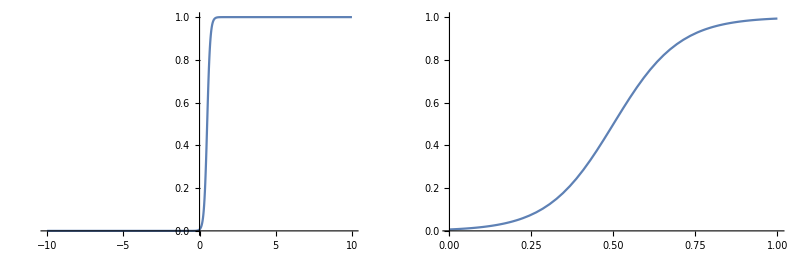

```mathematica
GraphicsRow[{Plot[f[g[x]],{x,-10,10},PlotRange->All,GridLines->{{1/2},{1/2}}],Plot[f[g[x]],{x,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2},{1/2}}]}]
```

```mathematica
f[g[x]]
```

LogisticSigmoid[5 (-1+2 x)]

```mathematica
(*
Manipulate[With[{
na=HardNeuralAND[{w}],
no=HardNeuralOR[{w}]
},
GraphicsRow[{
Plot[na[{b}],{b,0,1},PlotRange->{{0,1},{0,1}},Frame->True,GridLines->{{1/2}, {1/2}}],
Plot[na[{b}],{b,0,1},PlotRange->{{0,1},{0,1}},Frame->True,GridLines->{{1/2},{1/2}}]
}]],
{w,0,1},
SynchronousUpdating->False,
SynchronousInitialization->False
]
*)
```

```mathematica
Manipulate[
GraphicsRow[{
Plot[HardIncludeAND[b,w],{b,0,1},PlotRange->{{0,1},{0,1}},Frame->True,GridLines->{{1/2}, {1/2}}],
Plot[HardIncludeOR[b,w],{b,0,1},PlotRange->{{0,1},{0,1}},Frame->True,GridLines->{{1/2},{1/2}}]
}],
{w,0,1}
]
```

```mathematica
Manipulate[GraphicsRow[{
Plot[HardIncludeAND[b,w],{w,0,1},PlotRange->{{0,1},{0,1}},Frame->True,GridLines->{{1/2}, {1/2}}],
Plot[HardIncludeOR[b,w],{w,0,1},PlotRange->{{0,1},{0,1}},Frame->True,GridLines->{{1/2},{1/2}}]
}],
{b,0,1}
]
```

```mathematica
HardNeuralNOT[b_,w_]:=1-w+b (2 w-1)
```

```mathematica
Manipulate[Plot[HardNeuralNOT[b,w],{b,0,1},PlotRange->{{0,1},{0,1}},Frame->True,GridLines->{{1/2}, {1/2}}],{w,0,1}]
```

```mathematica
HardIncludeAND[b,w]
```

If[w>1/2,If[b>1/2,b,(2 w-1) b+1-w],If[b>1/2,-2 w (1-b)+1,1-w]]

```mathematica
f[input_List]:=With[{min=Min[input],mean=Mean[input]},
If[min>1/2,
min,
min+mean(1/2-min)]
]
```

```mathematica
Manipulate[Plot[f[{x1,x2,x3,x4,x5}],{x1,0,1},PlotRange->{{0,1},{0,1}},GridLines->{{1/2},{1/2}}],{x2,0,1},{x3,0,1},{x4,0,1},{x5,0,1}]
```